#### Function for correcting the alpha angle due to not perfectly putting PS at the outer edges

```mathematica
alphafunc=Function[{y},180/π*ArcCos[(25^2+y^2+2*25^2-(25-y)^2)/(2*√2*25*√(25^2+y^2))]];
alphacorr=alphafunc[16.8];
```

#### Data input - all channels [corr_PSL2_(alt_base)_4deg_no smooth --> large intw (-20 +10), correction selection with small PS, alternative baseline, 4° rotation considered, no smoothing]

```mathematica
LSPosition={"C1","C2","R0","R1","R2","L0","L1","L2"};
Phi={-139.2,58.92,-56.29,-95.24,-1.461,142.9,-186.6,111};
PhiError={1.13,2.06,0.98,2.92,3.536,0.7,2.1,2.1};
Sigma={38.66,42.13,61.72,59.31,104.2,58.15,83.76,51.84};
SigmaError={1.75,2,1.62,5.07,1.9,1.04,10.53,2.6};
Radius=1;
Alpha={-135,45,-45,-90-alphacorr,0+alphacorr,135,-180+alphacorr,90-alphacorr}

PhiList=Table[{Phi[[i]]*Pi/180,Radius},{i,Length[Phi]}] ;(*converting to radian and giving a fixed radius*)
LSPositionL=Thread[{LSPosition,Large}];
```

{-135,45,-45,-101.099,11.0989,135,-168.901,78.9011}

```mathematica
Mean[Table[Around[Sigma[[n]],SigmaError[[n]]],{n,1,8}]]
```

62.51.6

#### Data input - even channels [corr_PSL2_(alt_base)_4deg_no smooth --> large intw (-20 +10), correction selection with small PS, alternative baseline, 4° rotation considered, no smoothing]

```mathematica
LSPosition={"C1","C2","R0","R1","R2","L0","L1","L2"};
Phi={-147.5,60,-85.91,-122.7,0,-199.1+360,187.4-360,114.6};
PhiError={2.7,3,2.1,4.5,10,1.5,4.1,3.9};
Sigma={56.06,80,55.35,111.9,160,78.76,66.21,54.37};
SigmaError={3.98,5,3.37,2.4,3,5.32,8.22,4.95};
Radius=1;
Alpha={-135,45,-45,-90-alphacorr,0+alphacorr,135,-180+alphacorr,90-alphacorr}

PhiList=Table[{Phi[[i]]*Pi/180,Radius},{i,Length[Phi]}] ;(*converting to radian and giving a fixed radius*)
LSPositionL=Thread[{LSPosition,Large}];
```

{-135,45,-45,-101.099,11.0989,135,-168.901,78.9011}

```mathematica
Mean[Table[Around[Sigma[[n]],SigmaError[[n]]],{n,1,8}]]
```

82.81.7

#### Data input - odd channels [corr_PSL2_(alt_base)_4deg_no smooth --> large intw (-20 +10), correction selection with small PS, alternative baseline, 4° rotation considered, no smoothing]

```mathematica
LSPosition={"C1","C2","R0","R1","R2","L0","L1","L2"};
Phi={-137.5,53.12,-46.48,-81.15,-6.144,137.3,163.9-360,107.1};
PhiError={2,1.95,0.94,3.37,2.872,0.7,2.8,2.4};
Sigma={42.87,37.18,70.86,60.07,98.07,61.49,86.4,56.78};
SigmaError={2.52,2.05,2.32,5.46,1.65,1.24,5.1,3.75};
Radius=1;
Alpha={-135,45,-45,-90-alphacorr,0+alphacorr,135,-180+alphacorr,90-alphacorr}

PhiList=Table[{Phi[[i]]*Pi/180,Radius},{i,Length[Phi]}] ;(*converting to radian and giving a fixed radius*)
LSPositionL=Thread[{LSPosition,Large}];
```

{-135,45,-45,-101.099,11.0989,135,-168.901,78.9011}

```mathematica
Mean[Table[Around[Sigma[[n]],SigmaError[[n]]],{n,1,8}]]
```

64.21.2

#### Data input [data from andrea; corr08, no smooth, big intw]

```mathematica
LSPosition={"C1","C2","R0","R1","R2","L0","L1","L2"};
Phi={-141.8,54.77,-48.89,-83.03,-13.9,136.6,162.2-360,108.7};
PhiError={1.2,2.15,2.36,1.8,3.4,1.1,1.2,1.8};
Sigma={48.3,44.8,54.56,70.48,52.7,47.07,56.29,54.98};
SigmaError={1.4,2.9,3.59,4.38,4.2,1.23,1.75,2.3};
Radius=1;
Alpha={-135,45,-45,-90,0,135,-180,90}

PhiList=Table[{Phi[[i]]*Pi/180,Radius},{i,Length[Phi]}] ;(*converting to radian and giving a fixed radius*)
LSPositionL=Thread[{LSPosition,Large}];
```

{-135,45,-45,-90,0,135,-180,90}

```mathematica
Mean[Table[Around[Sigma[[n]],SigmaError[[n]]],{n,1,8}]]
```

53.61.0

### Plotting of the polar plot

```mathematica
PhiPolarPlot=ListPolarPlot[List /@ PhiList, PlotMarkers->List/@LSPositionL,PolarAxes->Automatic,PolarAxesOrigin->{0,Radius+0.2}, PolarTicks->{"Degrees",Automatic},TicksStyle->Medium,PlotRange->1.5,PolarGridLines->Automatic,PlotLabel->Style[TraditionalForm[HoldForm["Corrected " OverBar[Subscript[ϕ,ew]]"[°]"]],Large],ImageSize->Large]
```

-Graphics-

### Plotting of the α-ϕ-Plot

{{-135,-142.48.},{45,55.45.},{-45,-49.55.},{-90,-83.70.},{0,-14.53.},{135,137.47.},{-180,-198.56.},{90,109.55.}}

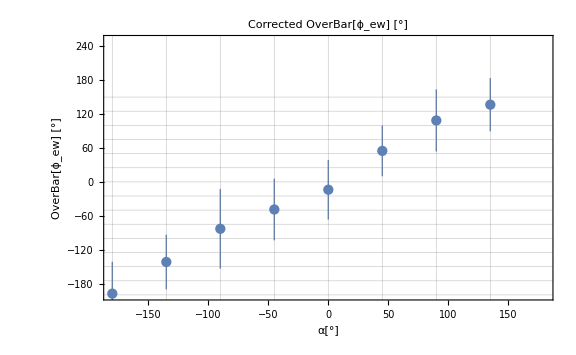

```mathematica
GridList=Table[i*25,{i,-200/25,150/25}];(*only for the graphic*)
AlphaPhiList=Table[{Alpha[[i]],Around[Phi[[i]],Sigma[[i]]]},{i,Length[Phi]}]
AlphaPhiPlot=ListPlot[AlphaPhiList,PlotRange->{{-180,180},{-200,250}},GridLines->{Alpha,GridList}, Axes->False,Frame->True, FrameTicksStyle->Medium, FrameLabel->{Style["α[°]",FontSize->16],Style[TraditionalForm[HoldForm[OverBar[Subscript[ϕ,ew]]"[°]"]],FontSize->16]},PlotLabel->Style[TraditionalForm[HoldForm["Corrected "OverBar[Subscript[ϕ,ew]]"[°]"]],Large], ImageSize->Large]
```

### Plotting the α-σ-Plot

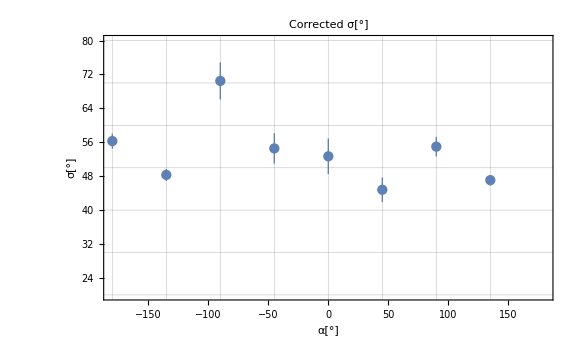

```mathematica
GridList=Table[i*10,{i,-200/25,150/10}];(*only for the graphic*)
AlphaSigmaList=Table[{Alpha[[i]],Around[Sigma[[i]],SigmaError[[i]]]},{i,Length[Sigma]}];
AlphaSigmaPlot=ListPlot[AlphaSigmaList,PlotRange->{{-180,180},{20,80}},GridLines->{Alpha,GridList}, Axes->False,Frame->True,FrameLabel->{"α[°]","σ[°]"},PlotLabel->Style["Corrected σ[°]",Large], ImageSize->Large]
```

## Klarifizierung des Konfidenzintervalls

{{-135,-141.8},{45,54.77},{-45,-48.89},{-90,-83.03},{0,-13.9},{135,136.6},{-180,-197.8},{90,108.7}}

FittedModel[-0.335338+1.06173 α]

-0.335338+1.06173 α-2.44691 √(1.3209+0.00120896 α+0.0000189895 α^2)

-0.335338+1.06173 α+2.44691 √(1.3209+0.00120896 α+0.0000189895 α^2)

-2.33018

2.96835

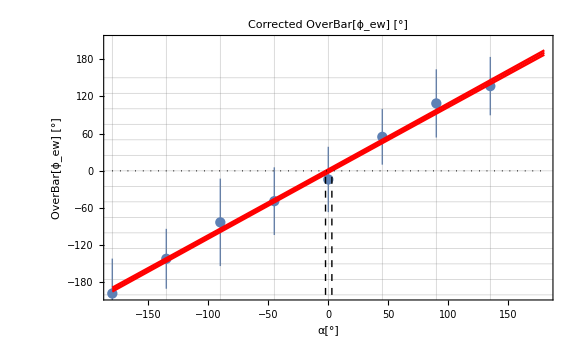

```mathematica
GridList=Table[i*25,{i,-200/25,150/25}];(*only for the graphic*)AlphaPhiPlot=ListPlot[AlphaPhiList,PlotRange->{{-180,180},{-200,210}},GridLines->{Alpha,GridList}, Axes->False,Frame->True,FrameLabel->{"α[°]",TraditionalForm[HoldForm[OverBar[Subscript[ϕ,ew]]"[°]"]]},PlotLabel->Style[TraditionalForm[HoldForm["Corrected "OverBar[Subscript[ϕ,ew]]"[°]"]],Large],ImageSize->Large];
AlphaPhiFitList=Table[{Alpha[[i]],Phi[[i]]},{i,Length[Phi]}]
fit=LinearModelFit[AlphaPhiFitList,α,α,Weights->1/PhiError^2,VarianceEstimatorFunction->(1&)]
LowerPredictionBand=fit["SinglePredictionBands"][[1]]
UpperPredictionBand=fit["SinglePredictionBands"][[2]]

AssumedPhi=0;
MinimumAlpha=Solve[UpperPredictionBand==AssumedPhi,α][[1,1,2]]
MaximumAlpha=Solve[LowerPredictionBand==AssumedPhi,α][[1,1,2]]

ErrorGraphic=Show[AlphaPhiPlot,
Plot[{fit["BestFit"],fit["SinglePredictionBands"]},{α,-180,180},PlotStyle->Red,Filling->{2->{1},3->{1}}],
Graphics[{Dashed,Line[{{MinimumAlpha,-200},{MinimumAlpha,AssumedPhi}}]}],
Graphics[{Dashed,Line[{{MaximumAlpha,-200},{MaximumAlpha,AssumedPhi}}]}],
Graphics[{Dotted,Line[{{-180,0},{180,0}}]}]]
(*Export["/home/alex/Dokumente/Studium/RootReader/RootAnalysis/couplingCorrection/ConfidencePlot.pdf",ErrorGraphic,"PDF"]*)
```

## Klarifizierung des Konfidenzintervalls 2

FittedModel[-0.335338+1.06173 α]

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.335338 | 0.566481 | -0.591967 | 0.575484
α | 1.06173 | 0.00435769 | 243.645 | 3.22587×10^-13

| DF | SS | MS | F-Statistic | P-Value
α | 1 | 59362.8 | 59362.8 | 1789.29 | 1.16802×10^-8
Error | 6 | 199.061 | 33.1768 |  | 
Total | 7 | 59561.8 |  |  |

0.996101

53.6475

7.96384

-57.2944+1.06173 α

56.6237+1.06173 α

-53.3317

53.9633

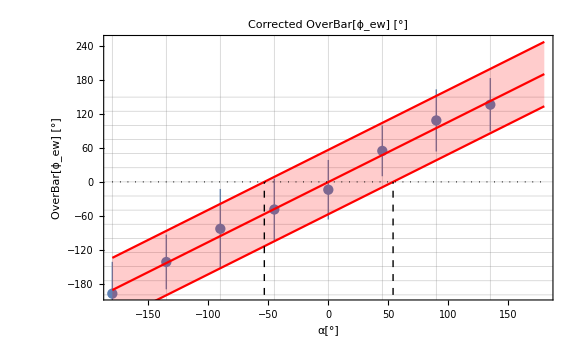

```mathematica
AlphaPhiPlot=ListPlot[AlphaPhiList,PlotRange->{{-180,180},{-200,250}},GridLines->{Alpha,GridList}, Axes->False,Frame->True,FrameTicksStyle->Medium,FrameLabel-> {Style["α[°]",FontSize->16],Style[TraditionalForm[HoldForm[OverBar[Subscript[ϕ,ew]]"[°]"]],FontSize->16]},PlotLabel->Style[TraditionalForm[HoldForm["Corrected "OverBar[Subscript[ϕ,ew]]"[°]"]],Large],ImageSize->Large];
AlphaPhiFitList=Table[{Alpha[[i]],Phi[[i]]},{i,Length[Phi]}];
fit=LinearModelFit[AlphaPhiFitList,α,α,Weights->1/PhiError^2,VarianceEstimatorFunction->(1&)]
fit["ParameterTable"]
fit["ANOVATable"]
fit["AdjustedRSquared"]
MeanSigma=Mean[Sigma]
StandardDeviation[Sigma]
LowerPredictionBand=fit["BestFit"];
UpperPredictionBand=fit["BestFit"];
LowerPredictionBand=LowerPredictionBand-fit["BestFitParameters"][[2]]*MeanSigma
UpperPredictionBand=UpperPredictionBand+fit["BestFitParameters"][[2]]*MeanSigma

AssumedPhi=0;
MinimumAlpha=Solve[UpperPredictionBand==AssumedPhi,α][[1,1,2]]
MaximumAlpha=Solve[LowerPredictionBand==AssumedPhi,α][[1,1,2]]

ErrorGraphic=Show[ListPlot[AlphaPhiList,PlotRange->{{-180,180},{-200,250}},GridLines->{Alpha,GridList}, Axes->False,Frame->True,FrameTicksStyle->Medium,FrameLabel-> {Style["α[°]",FontSize->16],Style[TraditionalForm[HoldForm[OverBar[Subscript[ϕ,ew]]"[°]"]],FontSize->16]},PlotLabel->Style[TraditionalForm[HoldForm["Corrected "OverBar[Subscript[ϕ,ew]]"[°]"]],Large],ImageSize->Large],
Plot[{fit["BestFit"],LowerPredictionBand,UpperPredictionBand},{α,-180,180},PlotStyle->Red,Filling->{2->{1},3->{1}}],
Graphics[{Dashed,Line[{{MinimumAlpha,-200},{MinimumAlpha,AssumedPhi}}]}],
Graphics[{Dashed,Line[{{MaximumAlpha,-200},{MaximumAlpha,AssumedPhi}}]}],
Graphics[{Dotted,Line[{{-180,0},{180,0}}]}],
PlotLabels->"Expressions"]
```